数组，或列表的列表

我们已经看到如何使用 Table 来创建列表。现在让我们看看如何使用 Table 来创建更高维的数组。

创建一个包含 4 个 x 的副本的列表：

```mathematica
Table[x,4]
```

{x,x,x,x}

创建包含 5 个 x 的列表的 4 份副本：

```mathematica
Table[x,4,5]
```

{{x,x,x,x,x},{x,x,x,x,x},{x,x,x,x,x},{x,x,x,x,x}}

使用 Grid 可以在网格中显示结果：

```mathematica
Grid[Table[x,4,5]]
```

x | x | x | x | x
x | x | x | x | x
x | x | x | x | x
x | x | x | x | x

你可以使用带有两个变量的 Table 来创建一个二维数组。第一个变量对应于行；第二个变量对应于列。

创建一个颜色数组，越向下颜色越红，越向右颜色越蓝：

```mathematica
Grid[Table[RGBColor[r,0,b],{r,0,1,.2},{b,0,1,.2}]]
```

RGBColor[0., 0, 0.] | RGBColor[0., 0, 0.2] | RGBColor[0., 0, 0.4] | RGBColor[0., 0, 0.6000000000000001] | RGBColor[0., 0, 0.8] | RGBColor[0., 0, 1.]
RGBColor[0.2, 0, 0.] | RGBColor[0.2, 0, 0.2] | RGBColor[0.2, 0, 0.4] | RGBColor[0.2, 0, 0.6000000000000001] | RGBColor[0.2, 0, 0.8] | RGBColor[0.2, 0, 1.]
RGBColor[0.4, 0, 0.] | RGBColor[0.4, 0, 0.2] | RGBColor[0.4, 0, 0.4] | RGBColor[0.4, 0, 0.6000000000000001] | RGBColor[0.4, 0, 0.8] | RGBColor[0.4, 0, 1.]
RGBColor[0.6000000000000001, 0, 0.] | RGBColor[0.6000000000000001, 0, 0.2] | RGBColor[0.6000000000000001, 0, 0.4] | RGBColor[0.6000000000000001, 0, 0.6000000000000001] | RGBColor[0.6000000000000001, 0, 0.8] | RGBColor[0.6000000000000001, 0, 1.]
RGBColor[0.8, 0, 0.] | RGBColor[0.8, 0, 0.2] | RGBColor[0.8, 0, 0.4] | RGBColor[0.8, 0, 0.6000000000000001] | RGBColor[0.8, 0, 0.8] | RGBColor[0.8, 0, 1.]
RGBColor[1., 0, 0.] | RGBColor[1., 0, 0.2] | RGBColor[1., 0, 0.4] | RGBColor[1., 0, 0.6000000000000001] | RGBColor[1., 0, 0.8] | RGBColor[1., 0, 1.]

将每个数组元素显示为行号：

```mathematica
Grid[Table[i,{i,4},{j,5}]]
```

1 | 1 | 1 | 1 | 1
2 | 2 | 2 | 2 | 2
3 | 3 | 3 | 3 | 3
4 | 4 | 4 | 4 | 4

将每个数组元素显示为列号：

```mathematica
Grid[Table[j,{i,4},{j,5}]]
```

1 | 2 | 3 | 4 | 5
1 | 2 | 3 | 4 | 5
1 | 2 | 3 | 4 | 5
1 | 2 | 3 | 4 | 5

生成一个数组，其中每个元素是其行号和列号之和：

```mathematica
Grid[Table[i+j,{i,5},{j,5}]]
```

2 | 3 | 4 | 5 | 6
3 | 4 | 5 | 6 | 7
4 | 5 | 6 | 7 | 8
5 | 6 | 7 | 8 | 9
6 | 7 | 8 | 9 | 10

创建一个乘法表：

```mathematica
Grid[Table[i*j,{i,5},{j,5}]]
```

1 | 2 | 3 | 4 | 5
2 | 4 | 6 | 8 | 10
3 | 6 | 9 | 12 | 15
4 | 8 | 12 | 16 | 20
5 | 10 | 15 | 20 | 25

ArrayPlot 可以让你对数组中的数值进行可视化。较大的值显示得更暗。

将乘法表可视化：

```mathematica
ArrayPlot[Table[i*j,{i,5},{j,5}]]
```

-Graphics-

生成并绘制一个随机值的数组：

```mathematica
ArrayPlot[Table[RandomInteger[10],30,30]]
```

-Graphics-

ArrayPlot 还可以让你把颜色作为值：

```mathematica
ArrayPlot[Table[RandomColor[ ],30,30]]
```

-Graphics-

图像本质上是由像素组成的数组。彩色图像使每个像素都有红色、绿色和蓝色值。黑白图像的像素值为 0(黑色)或 1(白色)。你可以使用 ImageData 来获得实际的像素值。

找出“W”的图像中的像素值：

```mathematica
ImageData[Binarize[ Rasterize["W"] ]]
```

{{1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1},{0,0,1,1,1,0,0,1,1,1,0,0},{1,0,1,1,1,0,0,1,1,1,0,1},{1,0,1,1,1,0,0,1,1,1,0,1},{1,0,1,1,0,0,0,0,1,1,0,1},{1,0,0,1,0,1,1,0,1,0,0,1},{1,0,0,1,0,1,1,0,1,0,1,1},{1,1,0,1,0,1,1,0,1,0,1,1},{1,1,0,0,0,1,1,0,0,0,1,1},{1,1,0,0,1,1,1,1,0,0,1,1},{1,1,0,0,1,1,1,1,0,0,1,1},{1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1}}

使用 ArrayPlot 来可视化数组的值：

```mathematica
ArrayPlot[ImageData[Binarize[ Rasterize["W"] ]]]
```

-Graphics-

这张图片的分辨率很低，因为 Rasterize 在这里就是这样创建的。它也是黑底白字，而不是白底黑字。这是因为在图像中，0 是黑色，1 是白色(就像在 RGBColor 中一样)，而 ArrayPlot 默认是使较大的数值较暗。

你可以用数组进行算术运算，就像列表一样。这意味着在这个数组中交换 0 和 1 很容易。只要用 1 减去所有东西，每个 0 就都变成了 1−0=1，而每个 1 都变成了 1−1=0。

找到像素值，然后进行算术运算，将数组中的 0 和 1 ：

```mathematica
1-ImageData[Binarize[ Rasterize["W"] ]]
```

{{0,0,0,0,0,0,0,0,0,0,0},{1,1,1,0,1,1,1,0,0,1,1},{0,1,1,0,0,1,0,0,0,1,0},{0,0,1,0,0,1,1,0,0,1,0},{0,0,1,0,0,1,1,0,0,0,0},{0,0,1,1,1,0,1,1,1,0,0},{0,0,0,1,1,0,0,1,1,0,0},{0,0,0,1,0,0,0,1,0,0,0},{0,0,0,1,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0}}

现在结果就是白底黑字了：

```mathematica
ArrayPlot[1-ImageData[Binarize[ Rasterize["W"] ]]]
```

-Graphics-

词汇

Table[x,4,5] |   | 创建 x 的二维数组
Grid[array] |   | 将数组中的值排列在一个网格中
ArrayPlot[array] |   | 可视化一个数组中的值
ImageData[image] |   | 从图像中获取像素值的数组

"共有 9 道习题"
"以及 2 道附加题" | "开始练习 »"

创建一个 12×12 的乘法表。»

| 期望输出： |  
  | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12
2 | 4 | 6 | 8 | 10 | 12 | 14 | 16 | 18 | 20 | 22 | 24
3 | 6 | 9 | 12 | 15 | 18 | 21 | 24 | 27 | 30 | 33 | 36
4 | 8 | 12 | 16 | 20 | 24 | 28 | 32 | 36 | 40 | 44 | 48
5 | 10 | 15 | 20 | 25 | 30 | 35 | 40 | 45 | 50 | 55 | 60
6 | 12 | 18 | 24 | 30 | 36 | 42 | 48 | 54 | 60 | 66 | 72
7 | 14 | 21 | 28 | 35 | 42 | 49 | 56 | 63 | 70 | 77 | 84
8 | 16 | 24 | 32 | 40 | 48 | 56 | 64 | 72 | 80 | 88 | 96
9 | 18 | 27 | 36 | 45 | 54 | 63 | 72 | 81 | 90 | 99 | 108
10 | 20 | 30 | 40 | 50 | 60 | 70 | 80 | 90 | 100 | 110 | 120
11 | 22 | 33 | 44 | 55 | 66 | 77 | 88 | 99 | 110 | 121 | 132
12 | 24 | 36 | 48 | 60 | 72 | 84 | 96 | 108 | 120 | 132 | 144 |

创建一个 5×5 的罗马数字乘法表。»

| 期望输出： |  
  | "I" | "II" | "III" | "IV" | "V"
"II" | "IV" | "VI" | "VIII" | "X"
"III" | "VI" | "IX" | "XII" | "XV"
"IV" | "VIII" | "XII" | "XVI" | "XX"
"V" | "X" | "XV" | "XX" | "XXV" |

创建一个 10×10 的随机颜色的网格。»

| 期望输出示例： |  
  | RGBColor[0.2686806675812221, 0.12895891413438165, 0.48612608778450617] | RGBColor[0.13677350825175116, 0.35655145450885906, 0.6175192436750943] | RGBColor[0.11603827689374602, 0.32929455571681876, 0.35363487796714166] | RGBColor[0.9594661026437363, 0.019174338408860736, 0.8638303296364533] | RGBColor[0.0023372194642738986, 0.5296844684311692, 0.8922657573759605] | RGBColor[0.5665018419385066, 0.062398458101144305, 0.7946395095949659] | RGBColor[0.1485067070533317, 0.878719460198053, 0.5145100781960741] | RGBColor[0.6986641480021518, 0.5277529931464182, 0.9882141989328659] | RGBColor[0.944470290299775, 0.5535549082540978, 0.5692362328538259] | RGBColor[0.9950288550859498, 0.6305255171534909, 0.14550245342878587]
RGBColor[0.47707565384127437, 0.6249071514987941, 0.25986435733448365] | RGBColor[0.5266744498730003, 0.5410779702989188, 0.4426300266010863] | RGBColor[0.6123265547206336, 0.550345301812746, 0.6292907613853804] | RGBColor[0.4683869383303483, 0.6376038999964784, 0.9482824036369504] | RGBColor[0.38839146046953865, 0.8865122076516063, 0.8202263600216109] | RGBColor[0.8773202310413715, 0.6362835701560172, 0.061260404202854835] | RGBColor[0.5588128127634175, 0.16248971289955483, 0.5766972867522775] | RGBColor[0.8511833587536144, 0.9070126840369901, 0.5390025527475242] | RGBColor[0.7506259318165425, 0.1312350628753729, 0.22332066944383255] | RGBColor[0.9774472795401823, 0.3187932574378307, 0.8399135077139674]
RGBColor[0.8659711441665874, 0.9337633437155759, 0.8284158906190038] | RGBColor[0.6813528961030477, 0.3116838246899687, 0.5261222571978508] | RGBColor[0.24953149181408607, 0.2700370274755417, 0.939270085452657] | RGBColor[0.39880452764619134, 0.11304137437881234, 0.9250643113223389] | RGBColor[0.722144192465362, 0.8141731175891291, 0.6054885055942887] | RGBColor[0.03510491575735286, 0.2251777828508641, 0.3320813121259285] | RGBColor[0.42071015332635664, 0.4475373562504277, 0.1139024756021787] | RGBColor[0.6693657848721715, 0.3331654119546559, 0.7234594637391647] | RGBColor[0.6959637718843776, 0.6580255185473778, 0.6401273378555634] | RGBColor[0.27801828448704513, 0.6976038656132033, 0.7682135474962679]
RGBColor[0.8050936353245965, 0.7795392042384779, 0.05856055453707354] | RGBColor[0.4821543050363186, 0.38700563675037003, 0.566044551763093] | RGBColor[0.5055334911414284, 0.031205725201232104, 0.47292037006274046] | RGBColor[0.8685490235605646, 0.9978119047515683, 0.0844149119888098] | RGBColor[0.844927124090106, 0.24617321712428142, 0.19296952872966888] | RGBColor[0.6381438817469831, 0.6400271534755568, 0.07726189879053225] | RGBColor[0.1487035205633498, 0.30422659858404955, 0.9660415960577498] | RGBColor[0.21093667672647975, 0.2847479238675159, 0.8195688125034541] | RGBColor[0.14108240863163646, 0.9087990701605684, 0.9538194144329759] | RGBColor[0.2768196546892643, 0.15368768179269643, 0.5382009355115158]
RGBColor[0.7736432092485326, 0.9056107663826616, 0.8772484432330501] | RGBColor[0.6177957558372875, 0.7375776492439312, 0.13393939980625924] | RGBColor[0.35214381279151064, 0.8639526997031575, 0.10865963128715062] | RGBColor[0.8699277500813425, 0.04136820346326098, 0.22194391878021413] | RGBColor[0.07384686737384416, 0.21033851150129346, 0.36168497841717784] | RGBColor[0.38837684824385565, 0.17672874225569735, 0.8804082745658994] | RGBColor[0.42677504026214197, 0.029970518394615953, 0.9093689137406216] | RGBColor[0.18874454935697726, 0.7706135696258611, 0.6861689229479895] | RGBColor[0.966908041371008, 0.3760517071812599, 0.7877995523073249] | RGBColor[0.9588642453966669, 0.9527506615610226, 0.6776685624701353]
RGBColor[0.07205227832990913, 0.2604184840349075, 0.7583535892561375] | RGBColor[0.18261855057037701, 0.07377077571605728, 0.9094641871448221] | RGBColor[0.039346983610691666, 0.7887535396336063, 0.6381457731138491] | RGBColor[0.36225527252229606, 0.278577547292733, 0.6267700051472707] | RGBColor[0.4144548264854313, 0.41726057846332854, 0.09312404235892613] | RGBColor[0.5999183979301403, 0.3848496420691847, 0.11890027599057218] | RGBColor[0.1382923672752192, 0.07817846911591331, 0.6881622733139259] | RGBColor[0.24624063780241556, 0.1800489249080821, 0.32849770905474385] | RGBColor[0.4685173932872393, 0.020378229002663284, 0.01003801403355098] | RGBColor[0.43787702587474797, 0.026595013928990996, 0.9451962960693305]
RGBColor[0.10271256838122578, 0.23402905207107216, 0.7124690719183648] | RGBColor[0.13574716529583064, 0.3852836779210671, 0.18069233382193683] | RGBColor[0.6594655586983071, 0.37226694738568766, 0.10523044882039057] | RGBColor[0.3016018675887575, 0.017367768024978636, 0.02988417913747421] | RGBColor[0.25744605732933556, 0.0009363281076462115, 0.4144185993777667] | RGBColor[0.6774781282708688, 0.34222154687598816, 0.9702957136604509] | RGBColor[0.25184011467250755, 0.1424666032202313, 0.08351853989844327] | RGBColor[0.9626986817854162, 0.4083796328498486, 0.8311777753095406] | RGBColor[0.6370847928517527, 0.9773515931950683, 0.5706929094966902] | RGBColor[0.8798007371690433, 0.2447981806185593, 0.997782208354512]
RGBColor[0.369233553307007, 0.625348557118919, 0.3122090291003854] | RGBColor[0.13515879780744156, 0.6771272543176945, 0.28193091711950724] | RGBColor[0.9060996386777893, 0.9560202893745733, 0.5085789630160067] | RGBColor[0.7304345932965026, 0.8615882113514635, 0.4099546416922448] | RGBColor[0.6207885604905226, 0.48777259529831696, 0.5545109977956224] | RGBColor[0.29599824564873267, 0.8436302159833555, 0.9412135524152723] | RGBColor[0.7909121435518047, 0.6208986403466146, 0.9436735191883905] | RGBColor[0.008032831548657304, 0.2176551315452826, 0.7476538249949745] | RGBColor[0.2434768809769423, 0.013672225061276855, 0.8698703822171678] | RGBColor[0.3491648958878386, 0.7132746264593937, 0.8641994206447752]
RGBColor[0.08648992316129767, 0.8603044846284271, 0.3652586767874819] | RGBColor[0.21434416032404568, 0.560445651410233, 0.9235747344420331] | RGBColor[0.6641969362359714, 0.8844412534660229, 0.7597163627298724] | RGBColor[0.7835349571323893, 0.7177206084208989, 0.9443621603773193] | RGBColor[0.4063999909281031, 0.1560001127426507, 0.9791487175568574] | RGBColor[0.1982275401878799, 0.5018874444551371, 0.7126747022344182] | RGBColor[0.46389356907610657, 0.9899568793510354, 0.18282549555593763] | RGBColor[0.7965448575036715, 0.2203076940626465, 0.8028855805437274] | RGBColor[0.9902733343532162, 0.25606104429275356, 0.3849896405954891] | RGBColor[0.6221007700303403, 0.01765127658624177, 0.22098467649124798]
RGBColor[0.8215044522625461, 0.16572454783069857, 0.8040773618551336] | RGBColor[0.24921899792850022, 0.2759862741314656, 0.9867270641108767] | RGBColor[0.9705600763758861, 0.6579222578247919, 0.09801587123491529] | RGBColor[0.5219662481223741, 0.14969988943827683, 0.21533096883363356] | RGBColor[0.2385598894514005, 0.420472814737084, 0.06616306125117433] | RGBColor[0.6189105535277344, 0.492652144492848, 0.2548520338813385] | RGBColor[0.2540039550834856, 0.25090544958492833, 0.7402121254547946] | RGBColor[0.033513046184048045, 0.1728855219836134, 0.026644850308877865] | RGBColor[0.6444793017816008, 0.8547066417937763, 0.3474794538334989] | RGBColor[0.16105684440590573, 0.0715923354102661, 0.15942531715860908] |

创建一个 10×10 的介于 0 到 10 之间的随机数字网格，每个元素的颜色也是随机的。»

| 期望输出示例： |  
  | 9 | 5 | 7 | 2 | 10 | 9 | 9 | 9 | 10 | 1
1 | 5 | 6 | 2 | 1 | 3 | 5 | 3 | 0 | 0
5 | 1 | 5 | 7 | 3 | 1 | 2 | 10 | 10 | 7
10 | 0 | 0 | 8 | 7 | 1 | 5 | 8 | 8 | 0
1 | 7 | 3 | 10 | 7 | 1 | 9 | 3 | 4 | 9
9 | 3 | 4 | 2 | 5 | 5 | 0 | 8 | 7 | 3
10 | 0 | 10 | 6 | 6 | 1 | 2 | 1 | 8 | 5
7 | 6 | 3 | 5 | 10 | 1 | 5 | 6 | 7 | 10
1 | 5 | 0 | 2 | 4 | 2 | 0 | 3 | 7 | 3
1 | 4 | 7 | 4 | 0 | 1 | 0 | 9 | 4 | 3 |

将所有可能的由两个字母组成的字符串(“aa”、“ab” 等等)做成一个网格。»

| 期望输出： |  
  | "aa" | "ab" | "ac" | "ad" | "ae" | "af" | "ag" | "ah" | "ai" | "aj" | "ak" | "al" | "am" | "an" | "ao" | "ap" | "aq" | "ar" | "as" | "at" | "au" | "av" | "aw" | "ax" | "ay" | "az"
"ba" | "bb" | "bc" | "bd" | "be" | "bf" | "bg" | "bh" | "bi" | "bj" | "bk" | "bl" | "bm" | "bn" | "bo" | "bp" | "bq" | "br" | "bs" | "bt" | "bu" | "bv" | "bw" | "bx" | "by" | "bz"
"ca" | "cb" | "cc" | "cd" | "ce" | "cf" | "cg" | "ch" | "ci" | "cj" | "ck" | "cl" | "cm" | "cn" | "co" | "cp" | "cq" | "cr" | "cs" | "ct" | "cu" | "cv" | "cw" | "cx" | "cy" | "cz"
"da" | "db" | "dc" | "dd" | "de" | "df" | "dg" | "dh" | "di" | "dj" | "dk" | "dl" | "dm" | "dn" | "do" | "dp" | "dq" | "dr" | "ds" | "dt" | "du" | "dv" | "dw" | "dx" | "dy" | "dz"
"ea" | "eb" | "ec" | "ed" | "ee" | "ef" | "eg" | "eh" | "ei" | "ej" | "ek" | "el" | "em" | "en" | "eo" | "ep" | "eq" | "er" | "es" | "et" | "eu" | "ev" | "ew" | "ex" | "ey" | "ez"
"fa" | "fb" | "fc" | "fd" | "fe" | "ff" | "fg" | "fh" | "fi" | "fj" | "fk" | "fl" | "fm" | "fn" | "fo" | "fp" | "fq" | "fr" | "fs" | "ft" | "fu" | "fv" | "fw" | "fx" | "fy" | "fz"
"ga" | "gb" | "gc" | "gd" | "ge" | "gf" | "gg" | "gh" | "gi" | "gj" | "gk" | "gl" | "gm" | "gn" | "go" | "gp" | "gq" | "gr" | "gs" | "gt" | "gu" | "gv" | "gw" | "gx" | "gy" | "gz"
"ha" | "hb" | "hc" | "hd" | "he" | "hf" | "hg" | "hh" | "hi" | "hj" | "hk" | "hl" | "hm" | "hn" | "ho" | "hp" | "hq" | "hr" | "hs" | "ht" | "hu" | "hv" | "hw" | "hx" | "hy" | "hz"
"ia" | "ib" | "ic" | "id" | "ie" | "if" | "ig" | "ih" | "ii" | "ij" | "ik" | "il" | "im" | "in" | "io" | "ip" | "iq" | "ir" | "is" | "it" | "iu" | "iv" | "iw" | "ix" | "iy" | "iz"
"ja" | "jb" | "jc" | "jd" | "je" | "jf" | "jg" | "jh" | "ji" | "jj" | "jk" | "jl" | "jm" | "jn" | "jo" | "jp" | "jq" | "jr" | "js" | "jt" | "ju" | "jv" | "jw" | "jx" | "jy" | "jz"
"ka" | "kb" | "kc" | "kd" | "ke" | "kf" | "kg" | "kh" | "ki" | "kj" | "kk" | "kl" | "km" | "kn" | "ko" | "kp" | "kq" | "kr" | "ks" | "kt" | "ku" | "kv" | "kw" | "kx" | "ky" | "kz"
"la" | "lb" | "lc" | "ld" | "le" | "lf" | "lg" | "lh" | "li" | "lj" | "lk" | "ll" | "lm" | "ln" | "lo" | "lp" | "lq" | "lr" | "ls" | "lt" | "lu" | "lv" | "lw" | "lx" | "ly" | "lz"
"ma" | "mb" | "mc" | "md" | "me" | "mf" | "mg" | "mh" | "mi" | "mj" | "mk" | "ml" | "mm" | "mn" | "mo" | "mp" | "mq" | "mr" | "ms" | "mt" | "mu" | "mv" | "mw" | "mx" | "my" | "mz"
"na" | "nb" | "nc" | "nd" | "ne" | "nf" | "ng" | "nh" | "ni" | "nj" | "nk" | "nl" | "nm" | "nn" | "no" | "np" | "nq" | "nr" | "ns" | "nt" | "nu" | "nv" | "nw" | "nx" | "ny" | "nz"
"oa" | "ob" | "oc" | "od" | "oe" | "of" | "og" | "oh" | "oi" | "oj" | "ok" | "ol" | "om" | "on" | "oo" | "op" | "oq" | "or" | "os" | "ot" | "ou" | "ov" | "ow" | "ox" | "oy" | "oz"
"pa" | "pb" | "pc" | "pd" | "pe" | "pf" | "pg" | "ph" | "pi" | "pj" | "pk" | "pl" | "pm" | "pn" | "po" | "pp" | "pq" | "pr" | "ps" | "pt" | "pu" | "pv" | "pw" | "px" | "py" | "pz"
"qa" | "qb" | "qc" | "qd" | "qe" | "qf" | "qg" | "qh" | "qi" | "qj" | "qk" | "ql" | "qm" | "qn" | "qo" | "qp" | "qq" | "qr" | "qs" | "qt" | "qu" | "qv" | "qw" | "qx" | "qy" | "qz"
"ra" | "rb" | "rc" | "rd" | "re" | "rf" | "rg" | "rh" | "ri" | "rj" | "rk" | "rl" | "rm" | "rn" | "ro" | "rp" | "rq" | "rr" | "rs" | "rt" | "ru" | "rv" | "rw" | "rx" | "ry" | "rz"
"sa" | "sb" | "sc" | "sd" | "se" | "sf" | "sg" | "sh" | "si" | "sj" | "sk" | "sl" | "sm" | "sn" | "so" | "sp" | "sq" | "sr" | "ss" | "st" | "su" | "sv" | "sw" | "sx" | "sy" | "sz"
"ta" | "tb" | "tc" | "td" | "te" | "tf" | "tg" | "th" | "ti" | "tj" | "tk" | "tl" | "tm" | "tn" | "to" | "tp" | "tq" | "tr" | "ts" | "tt" | "tu" | "tv" | "tw" | "tx" | "ty" | "tz"
"ua" | "ub" | "uc" | "ud" | "ue" | "uf" | "ug" | "uh" | "ui" | "uj" | "uk" | "ul" | "um" | "un" | "uo" | "up" | "uq" | "ur" | "us" | "ut" | "uu" | "uv" | "uw" | "ux" | "uy" | "uz"
"va" | "vb" | "vc" | "vd" | "ve" | "vf" | "vg" | "vh" | "vi" | "vj" | "vk" | "vl" | "vm" | "vn" | "vo" | "vp" | "vq" | "vr" | "vs" | "vt" | "vu" | "vv" | "vw" | "vx" | "vy" | "vz"
"wa" | "wb" | "wc" | "wd" | "we" | "wf" | "wg" | "wh" | "wi" | "wj" | "wk" | "wl" | "wm" | "wn" | "wo" | "wp" | "wq" | "wr" | "ws" | "wt" | "wu" | "wv" | "ww" | "wx" | "wy" | "wz"
"xa" | "xb" | "xc" | "xd" | "xe" | "xf" | "xg" | "xh" | "xi" | "xj" | "xk" | "xl" | "xm" | "xn" | "xo" | "xp" | "xq" | "xr" | "xs" | "xt" | "xu" | "xv" | "xw" | "xx" | "xy" | "xz"
"ya" | "yb" | "yc" | "yd" | "ye" | "yf" | "yg" | "yh" | "yi" | "yj" | "yk" | "yl" | "ym" | "yn" | "yo" | "yp" | "yq" | "yr" | "ys" | "yt" | "yu" | "yv" | "yw" | "yx" | "yy" | "yz"
"za" | "zb" | "zc" | "zd" | "ze" | "zf" | "zg" | "zh" | "zi" | "zj" | "zk" | "zl" | "zm" | "zn" | "zo" | "zp" | "zq" | "zr" | "zs" | "zt" | "zu" | "zv" | "zw" | "zx" | "zy" | "zz" |

为 {1,4,3,5,2} 创建饼状图、数轴图、线条图和条形图。把这些放在一个 2×2 的网格中。»

| 期望输出： |  
  | -Graphics- |

创建一个色相值为  x*y 的数组图，其中 x 和 y 分别为 0 到 1，步长为 0.05。»

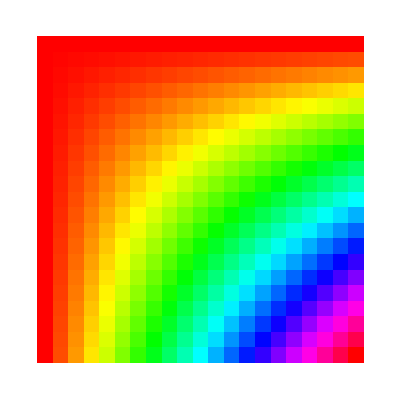
| 期望输出： |  
  | -Graphics- |

创建一个色相值为  x/y 的数组图，其中 x 和 y 分别为 1 到 50，步长为 1。»

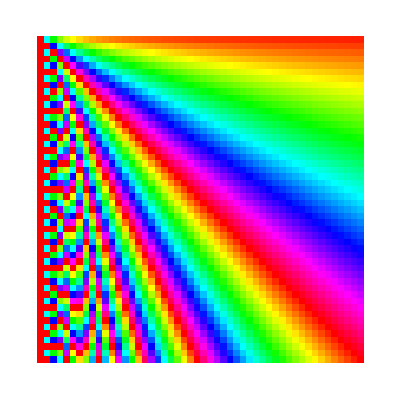
| 期望输出： |  
  | -Graphics- |

计算 100×100 以内的罗马数字乘法表，创建罗马数字长度的数组图。»

| 期望输出： |  
  | -Graphics- |

创建一个 20×20 的加法表。»

| 期望输出： |  
  | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21
3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22
4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23
5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24
6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25
7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26
8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27
9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28
10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29
11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30
12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31
13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32
14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33
15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34
16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35
17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36
18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37
19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38
20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39
21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 |

创建一个 10×10 的网格，元素为随机着色的 0 到 10 之间的随机整数，其字体大小为 32 以内的随机值。»

| 期望输出： |  
  | 6 | 9 | 2 | 5 | 6 | 6 | 4 | 2 | 6 | 1
8 | 7 | 10 | 8 | 4 | 3 | 1 | 3 | 3 | 6
0 | 7 | 0 | 3 | 8 | 9 | 10 | 3 | 10 | 7
4 | 10 | 1 | 5 | 1 | 3 | 1 | 1 | 5 | 10
0 | 10 | 0 | 4 | 5 | 5 | 4 | 7 | 4 | 8
1 | 6 | 6 | 8 | 9 | 2 | 9 | 1 | 0 | 5
5 | 0 | 7 | 10 | 2 | 6 | 3 | 7 | 0 | 3
9 | 10 | 4 | 9 | 10 | 2 | 3 | 6 | 2 | 1
10 | 7 | 4 | 5 | 2 | 0 | 2 | 3 | 3 | 9
8 | 4 | 2 | 10 | 10 | 9 | 8 | 2 | 6 | 5 |

问&答

表中一个变量的极值能否取决于另一个？

是的，后面的可以取决于前面的。Table[x,{i,4},{j,i}] 将创建一个“锯齿状”的三角形数组。

我可以把创建包含列表的列表的列表的表吗？

是的，你可以创建任意维度的表。Image3D 提供了一种将三维数组可视化的方法。

为什么在图像中 0 对应于黑色，1 对应于白色？

0 表示光的强度为零，即黑色。1 表示最大强度，即白色。

如何从 ImageData 的输出中取回原始图像？

只需对其应用函数 Image。

技术笔记

Wolfram 语言中的数组只是列表的列表。Wolfram 语言中也允许更通用的结构，即混合列表和其他东西。

Wolfram 语言中的列表对应于数学中的向量；等长的列表的列表则对应于矩阵。

如果一个数组中的大部分项都是 0(或其他固定值)，你可以使用 SparseArray 来构建一个数组，只需给出非零元素的位置和值。